## Log

PURPOSE: To make ‘gif’ 20f short video showing different colored tracked spots 
Red, Purple, Yel and White only 
07/27/2016 TM -- Updated the following features
			File format for saving all parameters was changed to Mathematica file from excel file.
			Reading in Parameters section was added.
			PairConnect3 was added. This function connects the nearest spot instead of the first encountered near enough spot.
				Slower than PairConnect2, about a double the speed, but there should not be error.
			PairConnect4 was added. This function gets rid of diversion of tracks.
			LinkTrack2 was added. This function gets rid of tracks which last shorter than threshold. And assign new track numbers.
				This avoids very big track numbers.

07/23/2016 TS -- Updated to match ParticleTracking_for_puro_2Colors.nb, which is what TM used in the Science translation paper. 

9/25/2015 TS -- Updated 3-color Find Red/Green/Blue Particles so that it shows the first “10” (endtest-starttest) and last “10” frames of movies to see if the threshold works well for the entire movie. 

11/15/2017 TS -- Now you can choose an option to highlight the binarized image on top of your original image when you are adjusting parameters for binarization. You can show either outline or filled in binarized image for this. 
This version also fixed a small bug regarding file name when you save tracks.

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

## Functions

### FitMySpotIntensity[img_,sigma_,dims_]

```mathematica
FitMySpotIntensity[img_,sigma_,dims_]:=Module[{myzs,my3Ddata,nlm,A,CC,x,x0,y,y0},
myzs=ImageData@img;
my3Ddata=Table[{i,j,myzs[[i,j]]},{i,1,dims,1},{j,1,dims,1}]//Flatten[#,1]&;
nlm=NonlinearModelFit[my3Ddata,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),{{CC,0},{x0,dims/2},{y0,dims/2},{A,0.5}},{x,y}];
{A/.nlm["BestFitParameters"],nlm["ParameterConfidenceIntervals"][[4]]}
]
```

### ImgCoord2DataCoord (integer)

```mathematica
Img2DataCoord[imageSize_,coordinate_]:=Module[{},
{#⟦2⟧,#⟦1⟧}&@Abs@({0,imageSize⟦2⟧+1}-Ceiling@coordinate)
]
```

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### MyThresholdingCrop (NEW - no rescale shit)

```mathematica
MyThresholdingCrop[img_,analysisFolder_, mytemplocs_, myPad_]:=Module[{myImg = img, myCrop},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
myImg ;
myCenterofCrop = { mytemplocs[[All,1]]//Median ,
mytemplocs[[All,2]]//Median  };


myCenterofVideoCropped = Table[  mytemplocs[[i]] - myCenterofCrop +{myPad + 0.1,myPad + 0.1},{i,1,Length@mytemplocs}];

mymessage = (*Test to see if any of the numbers GO OUTSIDE the pad: *)
 If [  
Cases[  Flatten@myCenterofVideoCropped,  x_/;x ≥ 2*myPad  || x<0 ]   == {} , 
"GOOD: all points are within pad size ", 
"Warning: the centroid goes out of the frame! "];

myCrop = Table[Table [ ImageTrim[myImg[[channel, time]], {#-myPad, #+myPad-0.1}&@ myCenterofCrop],{time, 1, Length@myImg[[1]],1}], {channel, 1, 3}];


Manipulate[
Column@{
mymessage,
Show[myCrop⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300]}, 
 
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myCrop⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thredcrop={threshold1,threshold2};
flagRed=ToString@thredcrop<>"Saved";
thredcrop>>analysisFolder<>"_thredcrop.dat"];
If[color==2,thgreencrop={threshold1,threshold2};flagGreen=ToString@thgreencrop<>"Saved";thgreencrop>>analysisFolder<>"_thgreencrop.dat"];
If[color==3,thbluecrop={threshold1,threshold2};flagBlue=ToString@thbluecrop<>"Saved";thbluecrop>>analysisFolder<>"_thbluecrop.dat"];
],
Spacer@5,
 
 
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredcrop,{threshold1,threshold2}=thredcrop];If[color==2&&ValueQ@thgreencrop,{threshold1,threshold2}=thgreencrop];If[color==3&&ValueQ@thbluecrop,{threshold1,threshold2}=thbluecrop]],
ControlPlacement->Left
]
]]
```

### MyThresholdingCropOLD

```mathematica
MyThresholdingCropOLD[img_,analysisFolder_, mytemplocs_, myPad_, myrescalefactor_]:=Module[{myImg = img, myCrop},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
myImg ;
myCenterofCrop = { mytemplocs[[All,1]]//Median ,
mytemplocs[[All,2]]//Median  };


myCenterofVideoCropped = Table[  mytemplocs[[i]] - myCenterofCrop +{myPad + 0.1,myPad + 0.1},{i,1,Length@mytemplocs}];

mymessage = (*Test to see if any of the numbers GO OUTSIDE the pad: *)
 If [  
Cases[  Flatten@myCenterofVideoCropped,  x_/;x ≥ 2*myPad  || x<0 ]   == {} , 
"GOOD: all points are within pad size ", 
"Warning: the centroid goes out of the frame! "];

myCrop = Table[Table[ ImageResize[ImageTrim[myImg[[channel, time]], {#-myPad, #+myPad-0.1}&@ myCenterofCrop],(2*myPad+1)*myRescaleFactor],{time, 1, Length@myImg[[1]],1}], {channel, 1, 3}];


Manipulate[
Column@{
mymessage,
Show[myCrop⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300]}, 
 
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myCrop⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thredcrop={threshold1,threshold2};
flagRed=ToString@thredcrop<>"Saved";
thredcrop>>analysisFolder<>"_thredcrop.dat"];
If[color==2,thgreencrop={threshold1,threshold2};flagGreen=ToString@thgreencrop<>"Saved";thgreencrop>>analysisFolder<>"_thgreencrop.dat"];
If[color==3,thbluecrop={threshold1,threshold2};flagBlue=ToString@thbluecrop<>"Saved";thbluecrop>>analysisFolder<>"_thbluecrop.dat"];
],
Spacer@5,
 
 
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredcrop,{threshold1,threshold2}=thredcrop];If[color==2&&ValueQ@thgreencrop,{threshold1,threshold2}=thgreencrop];If[color==3&&ValueQ@thbluecrop,{threshold1,threshold2}=thbluecrop]],
ControlPlacement->Left
]
]]
```

### MyThresholding

```mathematica
MyThresholding[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue.dat"),thblue=<<(analysisFolder<>"_thblue.dat");ToString@thblue<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,
"Blue Threshold : "<>flagBlue},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myImg⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];
If[color==3,thblue={threshold1,threshold2};flagBlue=ToString@thblue<>"Saved";thblue>>analysisFolder<>"_thblue.dat"];
],
Spacer@5,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];If[color==3&&ValueQ@thblue,{threshold1,threshold2}=thblue]],
ControlPlacement->Left
]
]]
```

```mathematica
MyThresholding3D[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue3D},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D.dat"),thblue3D=<<(analysisFolder<>"_thblue3D.dat");ToString@thblue3D<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦frame,z⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
(*"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,*)
"Blue Threshold 3D : "<>flagBlue3D},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
(*If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];*)
(*If[color==3,*)thblue3D={threshold1,threshold2};flagBlue3D=ToString@thblue3D<>"  Saved";thblue3D>>analysisFolder<>"_thblue3D.dat"(*]*);
],
Spacer@5,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];*)If[(*color==3&&*)ValueQ@thblue3D,{threshold1,threshold2}=thblue3D]],
ControlPlacement->Left
]
]]
```

### MyBinarization

```mathematica
MyBinarization[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue,max,imga,imgb,color,frame,threshold,lowpass,hipass,lo,hi,myOutline,myFill},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue2.dat"),thblueAll=<<(analysisFolder<>"_thblue2.dat");Append[ToString/@thblueAll,"Already Saved"],{"Not Yet Determined"}];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
imga=ImageAdjust[myImg⟦color,frame⟧, {0, 0, 1},threshold1⟦color⟧];
max=BandPass[ImageMultiply[ImageAdjust[myImg⟦color,1⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=SelectComponents[ImageMultiply[Binarize[BandPass[imga,{lowpass,hipass}],max threshold],mask],"Count",lo<#<hi&];
Column@{GraphicsRow[{Show[If[myOutline==True&&myFill==False,{imga,Graphics[{Green,#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2⟧},If[myFill==True,{imga,Graphics[{Green,Polygon@#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2,1,1⟧},imga]]],imgb},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],
Prepend[flagBlue,"Blue Threshold 2  :"]}},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Row@{"Display options: ",Spacer@5,"outline ",Checkbox[Dynamic@myOutline],Spacer@10,"filled ",Checkbox[Dynamic@myFill]},
Spacer@10,
Button["Save Threshold 2",
If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];
If[color==3,thblueAll={mymaxblue=max,thblue2=threshold,bandpassblue={lowpass,hipass},dotsizeblue={lo,hi}};
flagBlue=Append[ToString/@thblueAll,"Saved"];
thblueAll>>analysisFolder<>"_thblue2.dat"];
],
Spacer@10,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];If[color==3&&ValueQ@thblueAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblueAll]]
]]]
```

```mathematica
MyBinarization3D[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue3D,max,imgb,color,frame,threshold,lowpass,hipass,lo,hi},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D2.dat"),thblue3DAll=<<(analysisFolder<>"_thblue3D2.dat");Append[ToString/@thblue3DAll,"  Already Saved"],{"Not Yet Determined"}];
color=1;
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[max=BandPass[ImageMultiply[ImageAdjust[myImg⟦1,Round@(Length@myImg⟦1⟧/2)⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[ImageAdjust[myImg⟦frame,z⟧ , {0, 0, 1}, threshold1⟦color⟧],{lowpass,hipass}];
Column@{GraphicsRow[{ImageAdjust[myImg⟦frame,z⟧, {0, 0, 1},threshold1⟦color⟧],
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mask],"Count",lo<#<hi&]},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
(*Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],*)
Prepend[flagBlue3D,"Blue Threshold 3D 2  :"]}},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Button["Save Threshold 3D 2",
(*If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];*)
(*If[color==3,*)thblue3DAll={mymaxblue3D=max,thblue3D2=threshold,bandpassblue3D={lowpass,hipass},dotsizeblue3D={lo,hi}};
flagBlue3D=Append[ToString/@thblue3DAll,"  Saved"];
thblue3DAll>>analysisFolder<>"_thblue3D2.dat"(*];*)
],
Spacer@10,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];*)If[(*color==3&&*)ValueQ@thblue3DAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblue3DAll]]
]]]
```

### FindParticles

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],"Count",small<#<large&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticles[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,compResults},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&];
compResults=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
compResults⟦All,2⟧
]
```

```mathematica
(* After finding particles, add track number as 0, and add frame number *)
MyParticleFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
result=FindParticles[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧;
result=Table[Thread@{i,result⟦i⟧},{i,1,Length@result,1}];
result=Prepend[#,0]&/@#&/@result
]
```

```mathematica
FindGranuleMasks[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&]
]
```

```mathematica
myGranuleMaskFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
FindGranuleMasks[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input does not have color code such as {1,0,0} for red *)
ParticleFitting2[myColMovie_,channel_,mylongtracks_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
myTrimSize=2*pad+1;
Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
ParticleFitting3[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;

Table[
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[mySpots⟦frame,spot,2⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,frame+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,Length@Flatten@track1⟦1⟧]&; 
t2=track2//Flatten//Partition[#,Length@Flatten@track2⟦1⟧]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
t1⟦All,{1,2}⟧=t1⟦All,{2,1}⟧;
t2⟦All,{1,2}⟧=t2⟦All,{2,1}⟧;
ol={t1,t2}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### NearestNeighborLinking

```mathematica
(* Using a globally determined (automatic) threshod for binarization *)
NearestNeighborLinking1[img_,channel_,startFrame_,startPosition_,pad_,bandpass_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust@myTrimImg,bandpass]],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
(* Using user defined threshod for binarization *)
NearestNeighborLinking2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
NearestNeighborLinking3D2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

### ClickAndTrack

```mathematica
ClickAndTrack[imgRaw_,img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTrackNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];],
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames[StringDelete[#,DirectoryName@#]<>"_myTrack_"<>myColor<>"*",DirectoryName@#]&@analysisFolder;
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->150]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->150]]
}
}}]
]]
```

```mathematica
ClickAndTrack3D[(*imgRaw_,*)img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{(*"_thred2.dat","_thgreen2.dat",*)"_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];](*,
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

### FilterFitOutlier

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]
```

### SpotLocationOnCell

```mathematica
(* function to show cell movie with tracked spot positions *)
SpotLocationOnCell[myColMovie_,thred_,redSpots_,thgreen_,greenSpots_,thblue_,blueSpots_]:=Module[{th,colCircle,spots},
Manipulate[If[color==1,th=thred;colCircle=Red;spots=redSpots,
If[color==2,th=thgreen;colCircle=Green;spots=greenSpots,
th=thblue;colCircle=Blue;spots=blueSpots]];
Show[ImageAdjust[myColMovie⟦color,frame⟧,{0,0,1},th],Graphics[{colCircle,Circle[#,7]}&/@spots⟦frame⟧]],{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myColMovie⟦1⟧,1},ControlType->{RadioButtonBar,Automatic}]
]
```

### ShiftingDataPoints

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMin[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
myStart=(#-Min@#)+1&@Round@(10*myOffset);
myDataResample=Table[myDataInterpol⟦i,myStart⟦i⟧;;⟧,{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[myDataResample⟦i⟧,ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMean[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
(*myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;*)
myDataInterpol=Table[Array[myDataInterpolFunc⟦i⟧,1+myResolution*(Length@myData⟦i⟧-1),{1,Length@myData⟦i⟧}],{i,1,Length@myData,1}];
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset);
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[{myDataResample⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
myAllBlueNum
```

myAllBlueNum

```mathematica
ShiftingDataPointsMin[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
test=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myData=myAllBlueNum;
```

```mathematica
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
```

```mathematica
myDataInterpol=Array[#,1+10*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
```

```mathematica
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
```

```mathematica
test=myDataResample⟦All,;;All;;10⟧
```

{}

```mathematica
myFillSize=Max@#-#&@(Length/@test)
```

{}

```mathematica
myDataResample=Table[Flatten[Append[{test⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@test,1}]
```

{}

```mathematica
ConstantArray[{},]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},Null].

ConstantArray[{},Null]

```mathematica
Flatten[Append[{test⟦10⟧},ConstantArray[{},myFillSize⟦10⟧]],1]
```

Part::partw: Part 10 of {} does not exist.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},{}⟦10⟧].

{{}⟦10⟧,ConstantArray[{},{}⟦10⟧]}

```mathematica
myDataResample⟦10⟧
```

Part::partw: Part 10 of {} does not exist.

{}⟦10⟧

## Analysis

### Creating Transformation Function

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

Binarize::imginv: Expecting an image or graphics instead of myRefBeadsRedImg.

Binarize::imginv: Expecting an image or graphics instead of myRefBeadsGreenImg.

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

22 red particles and 21 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

General::munfl: 0.00146055^109.5 is too small to represent as a normalized machine number; precision may be lost.

{0.145887,TransformationFunction[(1.00153 | -0.00535795 | 1.65434
0.00333531 | 1.00279 | -1.17753
1.323×10^-6 | -1.97038×10^-6 | 1.)],Distance Before Correction | Distance After Correction
1.30654 | 0.268357
1.11552 | 0.169222
1.18853 | 0.12357
1.19209 | 0.184131
0.887496 | 0.106672
1.48898 | 0.137401
1.39806 | 0.138894
0.926871 | 0.11677
0.672956 | 0.0975416
1.51103 | 0.0653467
0.48527 | 0.214986
0.811439 | 0.176469
1.36392 | 0.132592
0.469058 | 0.116972
0.899135 | 0.157676
1.62771 | 0.08884
1.34893 | 0.137355
1.70638 | 0.121898
1.75108 | 0.121703
1.93512 | 0.247831
2.11636 | 0.1394}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.3,0.005}]
```

Binarize::imginv: Expecting an image or graphics instead of myCheckBeadsRedImg.

Binarize::imginv: Expecting an image or graphics instead of myCheckBeadsGreenImg.

Binarize::imginv: Expecting an image or graphics instead of myCheckBeadsRedImg.

Binarize::imginv: Expecting an image or graphics instead of myCheckBeadsGreenImg.

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

11 red particles and 12 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

General::munfl: 0.00136948^109.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00116798^109.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.78968×10^-307)/109.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Distance Before Correction | Distance After Correction
1.0694 | 0.211421
0.7065 | 0.31071
0.486721 | 0.360448
1.05229 | 0.252675
0.148912 | 0.359725
1.13515 | 0.160099
0.640942 | 0.181108
1.362 | 0.334306
1.73777 | 0.195666
1.38331 | 0.147089
1.51786 | 0.215895

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie0=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis/")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis/")];
analysisFolder=DirectoryName[mymovie]<>"Analysis/"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

```mathematica
myColMovie = myColMovie0;
```

### Reading in Parameters (if parameters exist)

#### basic parameters

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦2⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
mymask=-Graphics-;
(mymask//ImageDimensions) == {512,512}
Export[analysisFolder<>"_mask.tif",mymask];
```

True

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
If[FileExistsQ@(analysisFolder<>"_mask.tif"),"Mask File Exists","You Need to Make a Mask"]
```

Mask File Exists

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Tracking each particles w/ Click-and-Track function

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

## ClicknTrack Fit and export {X,Y} of white, yel, purp, and red example tracks

#### Red Tracks

Run “red tracks” once per track:

```mathematica
myRNAtrackFiles=FileNames["TA*_myTrack_red_13.dat",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_13.dat

```mathematica
analysisFolder2 = StringDrop[myRNAtrackFiles[[1]],-4]<> "_pur" (*Manually change this name to "wht, red, pur, yel" etc or however you want to classify your spots*)
```

/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_10_wht_myRedClickTracksCoordinates_pur

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myRNAtracks=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
```

```mathematica
mytemplocs = myRNAtracks[[1,All,3,1]] ;
(*mytemptimes=Table[i,{i,1,Length@myRNAtracks[[1,All,3,1]],1}]*)
frames = Length@myRNAtracks[[1]] ;
int = 1; 
mytemptimes = Table[i,{i,0,(frames*int)-1,int}] ;
myTimeList=mytemptimes +1 ;
```

```mathematica
{myRNAfits,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,myRNAtracks,5,1]; (*The centriod fits to the center movie of the average (rolling) frame*) (*RNAFits adds in fitted information and confidence interval about the centroid that we are fitting*)
```

```mathematica
Length/@myRNAfits
```

{20}

#### Red Crops

```mathematica
(*n=38;
mytemplocs[[n]]
myRedCenterList0[[n]]
```

```mathematica
myi=1;(*You have to change this depending on what track you are analyzing*)
```

```mathematica
myRNAfits⟦myi, All, 4, 1⟧;(*first track, all time points, fit information, coordinates of the centroid*)
```

```mathematica
myRedCenterList0=Ceiling@myRNAfits⟦myi, All, 4,1 ⟧;
```

```mathematica
myRedTrack = Table[Flatten@{mytemptimes[[i]], myRedCenterList0[[i]]},  {i,1,Length@mytemptimes -1,1}] ;
```

```mathematica
Show[ListPointPlot3D[Flatten/@Thread@{myRedTrack},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myRedTrack}]}],BoxRatios->{6,1,1},ImageSize->800]
```

-Graphics3D-

```mathematica
myRedCenterList =   myRedCenterList0
```

{{212,407},{212,406},{210,409},{208,408},{210,408},{211,408},{211,407},{211,407},{212,407},{212,408},{213,407},{213,408},{213,407},{213,408},{213,408},{212,408},{212,409},{212,409},{212,409},{212,409}}

```mathematica
myRedCenterList >> analysisFolder2<>"_myRedClickTracksCoordinates.dat"
```

## Make VIDEO crops of each track (Centered or tracked)

#### Import

```mathematica
myRNAtrackFiles=Table[
FileNames["TA10b_myTrack_red_*" <>{"wht*","yel*","pur*","_red*"}[[color]] ,DirectoryName@analysisFolder] , {color, 1,4,1}]
```

{{/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_10_wht_myRedClickTracksCoordinates.dat},{/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_12_yel_myRedClickTracksCoordinates.dat},{/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_13_pur_myRedClickTracksCoordinates.dat},{/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_myTrack_red_14_red_myRedClickTracksCoordinates.dat}}

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
Get@myRNAtrackFiles[[i,1]]
```

{{220,232},{221,232},{222,230},{223,231},{224,231},{222,230},{223,230},{223,230},{223,230},{223,230},{222,231},{220,230},{220,230},{221,231},{222,233},{221,232},{221,231},{221,230},{222,230},{220,231}}

```mathematica
myRedCenterList =Table[ Get[myRNAtrackFiles[[i,1]] ],{i,1,4}]
myTimeList = Range[1,Length@myRedCenterList[[1]]]
```

{{{220,232},{221,232},{222,230},{223,231},{224,231},{222,230},{223,230},{223,230},{223,230},{223,230},{222,231},{220,230},{220,230},{221,231},{222,233},{221,232},{221,231},{221,230},{222,230},{220,231}},{{337,227},{340,227},{339,228},{340,228},{340,230},{338,230},{340,230},{339,227},{338,228},{340,230},{343,232},{341,230},{341,231},{344,230},{345,229},{345,231},{345,231},{345,229},{343,229},{343,231}},{{212,407},{212,406},{210,409},{208,408},{210,408},{211,408},{211,407},{211,407},{212,407},{212,408},{213,407},{213,408},{213,407},{213,408},{213,408},{212,408},{212,409},{212,409},{212,409},{212,409}},{{360,279},{360,280},{359,281},{362,280},{362,281},{362,281},{360,287},{363,285},{364,286},{364,285},{365,286},{365,285},{368,282},{366,278},{367,279},{366,279},{365,280},{364,285},{365,288},{363,288}}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
myColorList = {"White","Yellow","Purple","Red"} ;
```

#### Determine Variables:

```mathematica
myPad = 512; 
myRescaleFactor = 1;
```

```mathematica
MyThresholdingCrop[myColMovie,analysisFolder2,myRedCenterList[[1]], myPad (*pad size*)]
```

```mathematica
MyThresholdingCrop[myColMovie,analysisFolder,myRedCenterList[[1]], myPad (*pad size*)];
mythresholds = {thredcrop, thgreencrop, thbluecrop};
myColMovieAdjusted = Table[ ImageAdjust[myColMovie[[th,i]],{0,0,1},mythresholds[[th]]], {th, 1, 3},{i,1,Length@myRedCenterList[[1]],1}] ;
```

```mathematica
myColMovieRGB = Table[ ColorCombine[myColMovieAdjusted[[All,i]]  ] ,{i,1,Length@myColMovieAdjusted[[1]]}];
myColMovieChannelsAndRGB = Transpose[Table[ Flatten@{myColMovieAdjusted[[All,i]],myColMovieRGB[[i]]} , {i,1,Length@myColMovieAdjusted[[1]]}]];
```

#### Make a video with White, Yellow, Purple and Red only spots called out with targets

```mathematica
myPad = 512;
```

```mathematica
mytemplocs = myRedCenterList[[1]];
mytemplocs//Length
```

20

```mathematica
myCenterofCrop = Ceiling/@{ myRedCenterList[[All,1]]//Median ,
myRedCenterList[[All,2]]//Median  }
myCenterofVideoCropped = Table[  mytemplocs[[i]] - myCenterofCrop +{myPad + 0.1,myPad + 0.1},{i,1,Length@mytemplocs}];
```

{{279,256},{281,256}}

```mathematica
(*Test to see if any of the numbers GO OUTSIDE the pad: *)
mymessage =  If [  
Cases[  Flatten@myCenterofVideoCropped,  x_/;x ≥ 2*myPad  || x<0 ]   == {} , 
"GOOD: points are within pad size 
", 
"Warning: Some of the spots go out of the frame! 
"]
```

GOOD: points are within pad size

RGB color combine dynamic image with tracking ring 
Image of the WHOLE CELL:

```mathematica
myLabel = Text@"iv.";
```

```mathematica
myRedCenterList[[1,frame]]
```

{224,231}

```mathematica
myRedCenterList[[1,frame]] + {5,5}
```

{229,236}

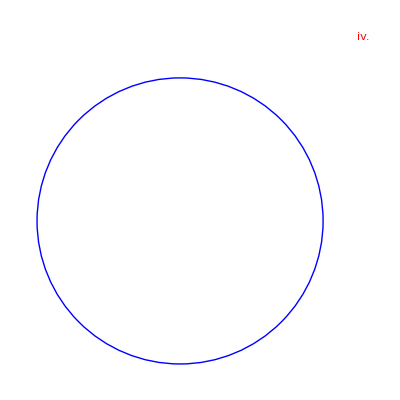

```mathematica
circle = Graphics[ { Text[ Style["iv.",Large,Red,FontFamily->"Arial Narrow"], myRedCenterList[[1,frame]]+ {9,9} ],Blue, Thick,Circle[  myRedCenterList[[1,frame]],7]}]
```

```mathematica
mytempspotvideotracked = Table[ Show[myColMovieAdjCrop[[frame]]   ,   
Graphics[ { Text[ Style["i.",Large,White,FontFamily->"Arial Narrow"], myRedCenterList[[1,frame]]+ {9,9} ],GrayLevel[1], Thick,Circle[  myRedCenterList[[1,frame]],7]}] , 
Graphics[ {Text[ Style["ii.",Large,White,FontFamily->"Arial Narrow"], myRedCenterList[[2,frame]]+ {9,9} ],   GrayLevel[1],Thick, Circle[  myRedCenterList[[2,frame]],7]}],
Graphics[ {Text[ Style["iii.",Large,White,FontFamily->"Arial Narrow"], myRedCenterList[[3,frame]]+ {9,9} ],  GrayLevel[1],Thick,  Circle[  myRedCenterList[[3,frame]],7]}],
Graphics[ {Text[ Style["iv.",Large,White,FontFamily->"Arial Narrow"], myRedCenterList[[4,frame]]+ {9,9} ],   GrayLevel[1],Thick, Circle[  myRedCenterList[[4,frame]],7]}] , 
     ImageSize-> 512*2] , {frame,1,20,1}]   ;
```

```mathematica
(*video of spot in whole cell*)
Manipulate[
Show[myColMovieAdjCrop[[frame]]   , Graphics[ {White, Thick,Circle[  myRedCenterList[[1,frame]],7]}],
Graphics[ {Yellow,Thick, Circle[  myRedCenterList[[2,frame]],7]}],
Graphics[ {RGBColor[0.63, 0, 1],Thick,  Circle[  myRedCenterList[[3,frame]],7]}],
Graphics[ {Red,Thick, Circle[  myRedCenterList[[4,frame]],7]}]    , ImageSize-> 512*2]
,{frame,1,Length@myTimeList,1}  ]
```

```mathematica
mytempspotvideotracked = Table[
Show[myColMovieAdjCrop[[frame]]   , Graphics[ {White, Thick,Circle[  myRedCenterList[[1,frame]],7]}],
Graphics[ {Yellow,Thick, Circle[  myRedCenterList[[2,frame]],7]}],
Graphics[ {RGBColor[0.63, 0, 1],Thick,  Circle[  myRedCenterList[[3,frame]],7]}],
Graphics[ {Red,Thick, Circle[  myRedCenterList[[4,frame]],7]}]    , ImageSize-> 512*2]
,{frame,1,Length@myTimeList,1}  ] ;
```

```mathematica
Export[ analysisFolder <> "_tracked_video.tiff", mytempspotvideotracked]
Export[ analysisFolder <> "_tracked_video_wholecell.avi", mytempspotvideotracked, "FrameRate" -> 4]
```

/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_tracked_video.tiff

/Volumes/BITTY/ExampleTACell_Fig1/Analysis/TA10b_tracked_video_wholecell.avi